# Analytical calculations for M = 1 (cont. time limit)

## 1. Computing changes in frequency due to selection

### Introduction

In the weak selection limit, the quantities we want to compute are

```mathematica
<Δ Subscript[x^sel, CC]>=<1/N∑_(i=1)^n Subscript[s, i,a] Subscript[s, i,d](Subscript[ω, i]^CC-1)>,<Δ Subscript[x^sel, CD]>=<1/N∑_(i=1)^n Subscript[s, i,a](1-Subscript[s, i,d])(Subscript[ω, i]^CD-1)>,
<Δ Subscript[x^sel, DC]>=<1/N∑_(i=1)^n (1-Subscript[s, i,a])Subscript[s, i,d](Subscript[ω, i]^DC-1)>,<Δ Subscript[x^sel, DC]>=<1/N∑_(i=1)^n (1-Subscript[s, i,a])(1-Subscript[s, i,d])(Subscript[ω, i]^DD-1)>                  (1)
```

where ω_i^s is the expected number of copies of individual i of strategy s due to selection and is given by

```mathematica
Subscript[ω, i]^s=(1-p/2)(Subscript[f, i]^s/(∑_j Subscript[f, j])-1/N) ≈(1-p/2)(β/N^3)(N Subscript[π, i]^s-∑_j Subscript[π, j])=(1-p/2)(β/N^3)Subscript[Y, i]^s
```

Thus, we first aim to compute the following quantities

```mathematica
<∑_(i=1)^n Subscript[s, i,a] Subscript[s, i,d](N Subscript[π, i]^CC-∑_j Subscript[π, j])> ,   <∑_(i=1)^n Subscript[s, i,a](1-Subscript[s, i,d])(N Subscript[π, i]^CD-∑_j Subscript[π, j])> ,   <∑_(i=1)^n (1-Subscript[s, i,a])Subscript[s, i,d](N Subscript[π, i]^DC-∑_j Subscript[π, j])> ,   <∑_(i=1)^n (1-Subscript[s, i,a])(1-Subscript[s, i,d])(N Subscript[π, i]^DD-∑_j Subscript[π, j])>          (2)
```

and then

### Defining payoffs

The general payoff function for M = 1 is given by

```mathematica
Subscript[π, i]=-Subscript[s, {i,a}](b-c)+1/2 ∑_(l=1)^n (b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}])+b (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l] (Subscript[s, {i,a}]-Subscript[s, {i,d}])-c (Subscript[s, {i,a}]+Subscript[s, {i,d}]))+(b-c) Subscript[s, {i,a}]
```

(b-c) s_{i,a}+1/2 ∑_(l=1)^n (-c h_i h_l (s_{i,a}-s_{i,d})-c (s_{i,a}+s_{i,d})+b h_i h_l (s_{l,a}-s_{l,d})+b (s_{l,a}+s_{l,d}))-s_{i,a}[b-c]

To compute the bracketed terms more easily, we first define the payoff function for each strategy:

```mathematica
ClearAll["Global`*"]
```

```mathematica
πgeneral[i_,sia_,sid_]:= (*sia,sid∈{0,1} to indicate strategy*)-(sia*Subscript[s, {i,a}])(b-c) + 1/2 ∑_(l=1)^n ExpandAll[(-c ((sia*Subscript[s, {i,a}])+(sid*Subscript[s, {i,d}]))+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, i] Subscript[h, l]((sia*Subscript[s, {i,a}])-(sid*Subscript[s, {i,d}]))+b Subscript[h, i] Subscript[h, l] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
```

```mathematica
πCC[i_]:=πgeneral[i,1,1]
πCD[i_]:=πgeneral[i,1,0] (*testing*)
πDC[i_]:=πgeneral[i,0,1]
πDD[i_]:=πgeneral[i,0,0]
```

```mathematica
πCC[i]
πCD[i]
πDC[i]
πDD[i]
```

-(b-c) s_{i,a}+1/2 ∑_(l=1)^n (-c s_{i,a}-c h_i h_l s_{i,a}-c s_{i,d}+c h_i h_l s_{i,d}+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

-(b-c) s_{i,a}+1/2 ∑_(l=1)^n (-c s_{i,a}-c h_i h_l s_{i,a}+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

1/2 ∑_(l=1)^n (-c s_{i,d}+c h_i h_l s_{i,d}+b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

1/2 ∑_(l=1)^n (b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})

For convenience, we define

```mathematica
(*use (1,1) for the summand since taking the average will take care of strategy frequency*)
Y[πstrat_,i_,n_]:=n*πstrat[i]-∑_(j=1)^n πgeneral[j,1,1]//ExpandAll
```

```mathematica
(*Example*)Y[πDD,i,n]
```

1/2 n ∑_(l=1)^n (b s_{l,a}+b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})-∑_(j=1)^n (-(b-c) s_{j,a}+1/2 ∑_(l=1)^n (-c s_{j,a}-c h_j h_l s_{j,a}-c s_{j,d}+c h_j h_l s_{j,d}+b s_{l,a}+b h_j h_l s_{l,a}+b s_{l,d}-b h_j h_l s_{l,d}))

### Defining rules

Next, we define some rules to simplify the summations:

```mathematica
(*rules for initial simplification*)
sumRule=Sum[expr1_,iter_]+Sum[expr2_,iter_]:>Sum[expr1+expr2,iter];
prodRule=Sum[expr1_,iter1_]*Sum[expr2_,iter2_]:>Sum[expr1*expr2,iter1,iter2];
revSumRule=Sum[expr1_+expr2_,iter_]:> Sum[expr1,iter]+Sum[expr2,iter];
constRule=Sum[c_?NumericQ  expr_,iter_]:>c Sum[expr,iter];
distRule=a_(b_+c_):>a*b+a*c;
dist2Rule=s_Subscript(b_+c_):>s*b+s*c;

miscRule=s_Subscript Sum[expr_,iter_]:> Sum[s*expr,iter];
squareRule = s_Subscript^2:>s;
unbracketRule=Sum[expr_,{i_,1,n}]:> n expr;

(*rules for collecting terms*)
mergeRule=a_ s1_Subscript s2_Subscript+b_ s1_Subscript s2_Subscript:> (FullSimplify[a+b])s1 s2;
```

### Simplifying expressions

We can now compute the expressions in (2) as

```mathematica
expandBracket[bracket_]:=ExpandAll[bracket]/.revSumRule/.constRule/.distRule//.miscRule//.distRule //.squareRule//.sumRule//.unbracketRule
```

```mathematica
xCCbracket:=expandBracket[Subscript[s, {i,a}] Subscript[s, {i,d}] Y[πCC,i,n] ]
xCDbracket:=expandBracket[Subscript[s, {i,a}](1-Subscript[s, {i,d}])Y[πCD,i,n]] 
xDCbracket:=expandBracket[(1-Subscript[s, {i,a}])Subscript[s, {i,d}] Y[πDC,i,n]]
xDDbracket:=expandBracket[(1-Subscript[s, {i,a}])(1-Subscript[s, {i,d}])Y[πDD,i,n]]
```

```mathematica
xCCbracket
xCDbracket
xDCbracket
xDDbracket
```

-b n s_{i,a} s_{i,d}+c n s_{i,a} s_{i,d}-1/2 c n^2 s_{i,a} s_{i,d}+n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 n^2 (-c s_{i,a} s_{i,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_i h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_i h_l s_{i,a} s_{i,d} s_{l,d})-1/2 n^2 (-c s_{i,a} s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,d}+c h_j h_l s_{i,a} s_{i,d} s_{j,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_j h_l s_{i,a} s_{i,d} s_{l,d})

-b n s_{i,a}+c n s_{i,a}-1/2 c n^2 s_{i,a}+b n s_{i,a} s_{i,d}-c n s_{i,a} s_{i,d}+1/2 c n^2 s_{i,a} s_{i,d}+n (b s_{i,a} s_{j,a}-c s_{i,a} s_{j,a})-n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 n^2 (-c h_i h_l s_{i,a}+b s_{i,a} s_{l,a}+b h_i h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d}-b h_i h_l s_{i,a} s_{l,d})-1/2 n^2 (-c s_{i,a} s_{j,a}-c h_j h_l s_{i,a} s_{j,a}-c s_{i,a} s_{j,d}+c h_j h_l s_{i,a} s_{j,d}+b s_{i,a} s_{l,a}+b h_j h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d}-b h_j h_l s_{i,a} s_{l,d})-1/2 n^2 (-c h_i h_l s_{i,a} s_{i,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_i h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_i h_l s_{i,a} s_{i,d} s_{l,d})+1/2 n^2 (-c s_{i,a} s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,d}+c h_j h_l s_{i,a} s_{i,d} s_{j,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_j h_l s_{i,a} s_{i,d} s_{l,d})

-1/2 c n^2 s_{i,d}+1/2 c n^2 s_{i,a} s_{i,d}+n (b s_{i,d} s_{j,a}-c s_{i,d} s_{j,a})-n (b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 n^2 (c h_i h_l s_{i,d}+b s_{i,d} s_{l,a}+b h_i h_l s_{i,d} s_{l,a}+b s_{i,d} s_{l,d}-b h_i h_l s_{i,d} s_{l,d})-1/2 n^2 (-c s_{i,d} s_{j,a}-c h_j h_l s_{i,d} s_{j,a}-c s_{i,d} s_{j,d}+c h_j h_l s_{i,d} s_{j,d}+b s_{i,d} s_{l,a}+b h_j h_l s_{i,d} s_{l,a}+b s_{i,d} s_{l,d}-b h_j h_l s_{i,d} s_{l,d})-1/2 n^2 (c h_i h_l s_{i,a} s_{i,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_i h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_i h_l s_{i,a} s_{i,d} s_{l,d})+1/2 n^2 (-c s_{i,a} s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,d}+c h_j h_l s_{i,a} s_{i,d} s_{j,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_j h_l s_{i,a} s_{i,d} s_{l,d})

-n (b s_{i,a} s_{j,a}-c s_{i,a} s_{j,a})-n (b s_{i,d} s_{j,a}-c s_{i,d} s_{j,a})+n (b s_{j,a}-c s_{j,a}+b s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,a})+1/2 b n^2 s_{l,a}-1/2 b n^2 s_{i,a} s_{l,a}-1/2 b n^2 s_{i,d} s_{l,a}+1/2 b n^2 s_{i,a} s_{i,d} s_{l,a}+1/2 n^2 (b h_i h_l s_{l,a}+b s_{l,d}-b h_i h_l s_{l,d})-1/2 n^2 (-c s_{j,a}-c h_j h_l s_{j,a}-c s_{j,d}+c h_j h_l s_{j,d}+b s_{l,a}+b h_j h_l s_{l,a}+b s_{l,d}-b h_j h_l s_{l,d})-1/2 n^2 (b h_i h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d}-b h_i h_l s_{i,a} s_{l,d})+1/2 n^2 (-c s_{i,a} s_{j,a}-c h_j h_l s_{i,a} s_{j,a}-c s_{i,a} s_{j,d}+c h_j h_l s_{i,a} s_{j,d}+b s_{i,a} s_{l,a}+b h_j h_l s_{i,a} s_{l,a}+b s_{i,a} s_{l,d}-b h_j h_l s_{i,a} s_{l,d})-1/2 n^2 (b h_i h_l s_{i,d} s_{l,a}+b s_{i,d} s_{l,d}-b h_i h_l s_{i,d} s_{l,d})+1/2 n^2 (-c s_{i,d} s_{j,a}-c h_j h_l s_{i,d} s_{j,a}-c s_{i,d} s_{j,d}+c h_j h_l s_{i,d} s_{j,d}+b s_{i,d} s_{l,a}+b h_j h_l s_{i,d} s_{l,a}+b s_{i,d} s_{l,d}-b h_j h_l s_{i,d} s_{l,d})+1/2 n^2 (b h_i h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_i h_l s_{i,a} s_{i,d} s_{l,d})-1/2 n^2 (-c s_{i,a} s_{i,d} s_{j,a}-c h_j h_l s_{i,a} s_{i,d} s_{j,a}-c s_{i,a} s_{i,d} s_{j,d}+c h_j h_l s_{i,a} s_{i,d} s_{j,d}+b s_{i,a} s_{i,d} s_{l,a}+b h_j h_l s_{i,a} s_{i,d} s_{l,a}+b s_{i,a} s_{i,d} s_{l,d}-b h_j h_l s_{i,a} s_{i,d} s_{l,d})

#### Simplifying the CC term

First, we define rules for relabeling quantities that are equivalent (note that the order of substitution matters here).

```mathematica
subCC1={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCC2={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}] };
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4(1/n+(n-1)/n y)}; (*see the SI for definitions of y, z, g, h*)
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}] -> 1/4};
```

Then we can simplify the expression for CC as:

```mathematica
FullSimplify[xCCbracket]//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 // FullSimplify
```

1/4 (b+c (-1+n)) (-1+n) (-1+y)

#### Simplifying the CD term

```mathematica
subCD10={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subCD11={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subCD12={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subCD13={Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y)};
subCD14={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,a}]->1/2};
```

```mathematica
(*simplify*)
FullSimplify[xCDbracket]//.distRule//.subCD10//.subCD11//.subCD12//.subCD13//.subCD14//FullSimplify
```

1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

#### Simplifying the DC term

```mathematica
subDC5={ Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}],
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]};
subDC6={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}],
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {i,d}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,a}]->1/4 Subscript[h, i] Subscript[h, l],(*disguised z*)
		Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}],(*duplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {j,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}],(*triplet*)
		Subscript[h, j] Subscript[h, l] Subscript[s, {i,d}] Subscript[s, {l,d}]->Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}](*triplet*)};
subDC7={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2*1/2(1/n+(n-1)/n y),Subscript[h, i] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),Subscript[h, j] Subscript[h, l] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y))};
subDC8={Subscript[h, i] Subscript[h, l] Subscript[s, {i,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y)};
subDC9={Subscript[h, i] Subscript[h, l]-> 1/n+(n-1)/n z,Subscript[s, {i,d}]->1/2};
```

```mathematica
(*simplify*)
FullSimplify[xDCbracket]//.distRule//.subDC5//.subDC6//.subDC7//.subDC8//.subDC9// FullSimplify
```

-1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

#### Simplifying the DD term

```mathematica
(*we combine the simplifications from CD and DC*)
subDD15={Subscript[h, j] Subscript[h, l] Subscript[s, {j,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {j,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,a}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[h, i] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],Subscript[h, j] Subscript[h, l] Subscript[s, {l,d}]-> 1/2 Subscript[h, i] Subscript[h, l],
		Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2(1/n+(n-1)/n y),
		Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/4,Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4};
subDD16={Subscript[s, {j,a}]->1/2,Subscript[s, {j,d}]->1/2};
```

```mathematica
(*simplify*)
FullSimplify[xDDbracket]//.distRule//.subDC5//.subCD10//.subDC6//.subCD11//.subDC7//.subDD15//.subDD16//FullSimplify
```

-1/4 (b+c (-1+n)) (-1+n) (-1+y)

### Summary: bracket terms in terms of y, z, g, h

```mathematica
xCCbracket2:=FullSimplify[xCCbracket]//.distRule//.subCC1//.subCC2//.subCC3//.subCC4 // FullSimplify
xCDbracket2:=FullSimplify[xCDbracket]//.distRule//.subCD10//.subCD11//.subCD12//.subCD13//.subCD14//FullSimplify
xDCbracket2:=FullSimplify[xDCbracket]//.distRule//.subDC5//.subDC6//.subDC7//.subDC8//.subDC9// FullSimplify
xDDbracket2:=FullSimplify[xDDbracket]//.distRule//.subDC5//.subCD10//.subDC6//.subCD11//.subDC7//.subDD15//.subDD16//FullSimplify
```

```mathematica
xCCbracket2
xCDbracket2
xDCbracket2
xDDbracket2
(*ΔxCCinf[n_,β_,p_,b_,c_,μ_,ν_]=xCCbracket2/.{n-1->n,n-2->n}/.{b+c n->n}/.{y->yeval[μ,ν],g->geval[μ,ν],h->heval[μ,ν]}//FullSimplify
ΔxCDinf[n_,β_,p_,b_,c_,μ_,ν_]=xCDbracket2/.{n-1->n,n-2->n}/.{-a_ n+a_->-a n}/.{d_+n e_->e n}/.{y->yeval[μ,ν],g->geval[μ,ν],h->heval[μ,ν]}//FullSimplify
ΔxDCinf[n_,β_,p_,b_,c_,μ_,ν_]=xDCbracket2/.{n-1->n,n-2->n}/.{-a_ n+a_->-a n}/.{d_+n e_->e n}/.{y->yeval[μ,ν],g->geval[μ,ν],h->heval[μ,ν]}//FullSimplify
ΔxDDinf[n_,β_,p_,b_,c_,μ_,ν_]=xDDbracket2/.{n-1->n,n-2->n}/.{b+c n->n}/.{y->yeval[μ,ν],g->geval[μ,ν],h->heval[μ,ν]}//FullSimplify*)
```

1/4 (b+c (-1+n)) (-1+n) (-1+y)

1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

-1/4 (-1+n) (-b (g+h (-2+n)-g n+z)+c (g+h (-2+n)+z-n z))

-1/4 (b+c (-1+n)) (-1+n) (-1+y)

Check that the sum of these expressions is zero:

```mathematica
xCCbracket2 + xCDbracket2 + xDCbracket2 + xDDbracket2==0
```

True

## 2. Computing y, z, g, h in the continuous time limit

To simplify the above expressions, we need to compute the quantities y, z, g, and h as defined in the SI.

### Define functions related to coalescence time

```mathematica
γ[n_,p_]:=1-(n*p)/(2(n-1))
tt[τ_,n_,p_]:=τ*(n^2/(2γ[n,p]))
ρ[τ_,p_]:=Exp[-τ]
ρ2[τ3_,τ2_]:=3*Exp[-3*τ3]Exp[-τ2]
```

### Compute y

```mathematica
yt[t_,n_,p_,u_]:=1/2(1+(1-u/n γ[n,p])^(2*t)) (*from the SI*)
```

We then take the limit after replacing t=τ*(n^2/(2(1-p/2))) and u = μ / n:

```mathematica
ytau[μ_,τ_,p_]:=Limit[yt[tt[τ,n,p],n,p,μ/n],n->Infinity]
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
Print["Check: ",yt[tt[τ,n,p],n,p,μ/n]//FullSimplify," ---> ",ytau[μ,τ,p]]
```

Check: 1/2 (1+(1-((1+(n p)/(2-2 n)) μ)/n^2)^(-(2 (-1+n) n^2 τ)/(2+n (-2+p)))) ---> 1/2 (1+ⅇ^(-μ τ))

We will also define a function to compute the integrals more quickly :

```mathematica
yeval[μ_,ν_]=y[μ,p];
ycalc[n_,u_,v_]=y[μ,p]/.{μ->n*u};
```

```mathematica
Print[yeval[μ,ν]," or ",ycalc[n,u,v]]
```

(2+μ)/(2+2 μ) or (2+n u)/(2+2 n u)

### Compute z

```mathematica
zt[t_,n_,p_,v_]:=(1-v/n γ[n,p])^(2*t)
```

We then take the limit after replacing t=τ*(n^2/(2γ))and v=ν/n

```mathematica
ztau[ν_,τ_,p_]:=Limit[zt[tt[τ,n,p],n,p,ν/n],n->Infinity]
z[ν_,p_]:=Integrate[ztau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
zeval[μ_,ν_]=z[ν,p]// FullSimplify;
zcalc[n_,u_,v_]=z[ν,p]/.{ν->n*v} // FullSimplify;
```

```mathematica
Print["Check: ",zt[tt[τ,n,p],n,p,ν/n]//FullSimplify," ---> ",ztau[ν,τ,p]]
Print[zeval[μ,ν]," or ",zcalc[n,u,v]]
```

Check: (1-((1+(n p)/(2-2 n)) ν)/n^2)^(-(2 (-1+n) n^2 τ)/(2+n (-2+p))) ---> ⅇ^(-ν τ)

1/(1+ν) or 1/(1+n v)

### Compute g

```mathematica
gtau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*ztau[ν,τ,p]
g[μ_,ν_,p_]:=Integrate[gtau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
geval[μ_,ν_]=g[μ,ν,p] // FullSimplify;
gcalc[n_,u_,v_]=g[μ,ν,p]/.{ν->n*v,μ->n*u}// FullSimplify;
```

```mathematica
Print["Check: ",gtau[μ,ν,τ,p]]
Print[geval[μ,ν]," or ",gcalc[n,u,v]]
```

Check: 1/2 ⅇ^(-ν τ) (1+ⅇ^(-μ τ))

1/2 (1/(1+ν)+1/(1+μ+ν)) or 1/2 (1/(1+n v)+1/(1+n (u+v)))

### Compute h

```mathematica
htau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*ztau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3+τ2,p])
h[μ_,ν_,p_]:=Integrate[htau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ2,0,Infinity},{τ3,0,Infinity}][[1]]
heval[μ_,ν_]=h[μ,ν,p] // FullSimplify//Apart;
hcalc[n_,u_,v_]=h[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
```

```mathematica
Print["Check: ",htau[μ,ν,τ3,τ2,p]]
Print[heval[μ,ν]," or ",hcalc[n,u,v]]
```

Check: 1/3 (1/2 ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ τ3))+1/2 ⅇ^(-ν τ2) (1+ⅇ^(-μ (τ2+τ3)))+1/2 ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ (τ2+τ3))))

(11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν)) or (11+4 n u)/(6 (2+n u) (1+n v))-1/(2 (3+n v))+(5+n u)/(4 (3+n u) (1+n u+n v))+(-4-n u)/(4 (2+n u) (3+n u+n v))

### Compute theoretical predictions and export data

We compute the values of y, z, g, h for various values of v

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];

(*compute y,z,g,h for each v*)
data=Flatten[
Table[{u/.params,v,
ycalc[n,u,v]/.params,zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params},
{v,vs}],
0]; (*flatten into a data table*)
headers={"u","v","y","z","g","h"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/data/calc_data/calc_data.csv"; (*change as needed*)
(*Export[filename,data]*)
```

```mathematica
data
```

{{u,v,y,z,g,h},{0.001,0.001,0.980769,0.961538,0.943732,0.935249},{0.001,0.00149535,0.980769,0.943562,0.926403,0.914037},{0.001,0.00223607,0.980769,0.9179,0.901646,0.883833},{0.001,0.0033437,0.980769,0.88203,0.867001,0.841773},{0.001,0.005,0.980769,0.833333,0.819892,0.784999},{0.001,0.00747674,0.980769,0.769782,0.758284,0.711551},{0.001,0.0111803,0.980769,0.690983,0.681691,0.621685},{0.001,0.0167185,0.980769,0.599254,0.59224,0.519158},{0.001,0.025,0.980769,0.5,0.495098,0.411507},{0.001,0.0373837,0.980769,0.400746,0.397584,0.308473},{0.001,0.0559017,0.980769,0.309017,0.30713,0.218936},{0.001,0.0835925,0.980769,0.230218,0.229168,0.148079},{0.001,0.125,0.980769,0.166667,0.166115,0.0965029},{0.001,0.186919,0.980769,0.11797,0.117693,0.0614246},{0.001,0.279508,0.980769,0.0820995,0.0819651,0.0386959},{0.001,0.417963,0.980769,0.0564382,0.0563746,0.0243834},{0.001,0.625,0.980769,0.0384615,0.038432,0.0154707}}

### Summary: y, z, g, h

In summary we have

```mathematica
yeval[μ,ν]
zeval[μ,ν]
geval[μ,ν]
heval[μ,ν]
```

(2+μ)/(2+2 μ)

1/(1+ν)

1/2 (1/(1+ν)+1/(1+μ+ν))

(11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν))

## 3. Computing strategy frequencies

### Computing the full bracketed terms

We define the following functions to compute the original bracketed terms in (1):

```mathematica
Clear[nn,β,p,bb,cc,μ,ν];
ΔxCC[nn_,β_,p_,bb_,cc_,μ_,ν_]=(1-p/2)(β/nn^3)xCCbracket2/.{n->nn,b->bb,c->cc,y->yeval[μ,ν](*,z->zeval[μ,ν], g-> geval[μ,ν],h-> heval[μ,ν]*)};
ΔxCD[nn_,β_,p_,bb_,cc_,μ_,ν_]=(1-p/2)(β/nn^3)xCDbracket2/.{n->nn,b->bb,c->cc,y-> yeval[μ,ν],z->zeval[μ,ν],g-> geval[μ,ν],h-> heval[μ,ν]};
ΔxDC[nn_,β_,p_,bb_,cc_,μ_,ν_]=(1-p/2)(β/nn^3)xDCbracket2/.{n->nn,b->bb,c->cc,y-> yeval[μ,ν],z->zeval[μ,ν],g-> geval[μ,ν],h-> heval[μ,ν]};
ΔxDD[nn_,β_,p_,bb_,cc_,μ_,ν_]=(1-p/2)(β/nn^3)xDDbracket2/.{n->nn,b->bb,c->cc,y-> yeval[μ,ν](*,z-> zeval[μ,ν],g->geval[μ,ν],h-> heval[μ,ν]*)};
```

The expressions look like:

```mathematica
ΔxCC[n,β,p,b,c,μ,ν]
ΔxCD[n,β,p,b,c,μ,ν]
ΔxDC[n,β,p,b,c,μ,ν]
ΔxDD[n,β,p,b,c,μ,ν]
```

((b+c (-1+n)) (-1+n) (1-p/2) β (-1+(2+μ)/(2+2 μ)))/(4 n^3)

1/(4 n^3)(-1+n) (1-p/2) β (c (1/(1+ν)-n/(1+ν)+1/2 (1/(1+ν)+1/(1+μ+ν))+(-2+n) ((11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν))))-b (1/(1+ν)+1/2 (1/(1+ν)+1/(1+μ+ν))-1/2 n (1/(1+ν)+1/(1+μ+ν))+(-2+n) ((11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν)))))

-1/(4 n^3)(-1+n) (1-p/2) β (c (1/(1+ν)-n/(1+ν)+1/2 (1/(1+ν)+1/(1+μ+ν))+(-2+n) ((11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν))))-b (1/(1+ν)+1/2 (1/(1+ν)+1/(1+μ+ν))-1/2 n (1/(1+ν)+1/(1+μ+ν))+(-2+n) ((11+4 μ)/(6 (2+μ) (1+ν))-1/(2 (3+ν))+(5+μ)/(4 (3+μ) (1+μ+ν))+(-4-μ)/(4 (2+μ) (3+μ+ν)))))

-((b+c (-1+n)) (-1+n) (1-p/2) β (-1+(2+μ)/(2+2 μ)))/(4 n^3)

```mathematica
(*ΔxCCinf[n_,β_,p_,b_,c_,μ_,ν_]=FullSimplify[ΔxCC[n,β,p,b,c,μ,ν]]/.{n-1->n}/.{b+c n->n}
ΔxCDinf[n_,β_,p_,b_,c_,μ_,ν_]=FullSimplify[ΔxCD[n,β,p,b,c,μ,ν]]/.{n-1->n}/.{b+c n->n}
ΔxDCinf[n_,β_,p_,b_,c_,μ_,ν_]=FullSimplify[ΔxDC[n,β,p,b,c,μ,ν]]/.{n-1->n}/.{b+c n->n}
ΔxDDinf[n_,β_,p_,b_,c_,μ_,ν_]=FullSimplify[ΔxDD[n,β,p,b,c,μ,ν]]/.{n-1->n}/.{b+c n->n}*)
```

0.04

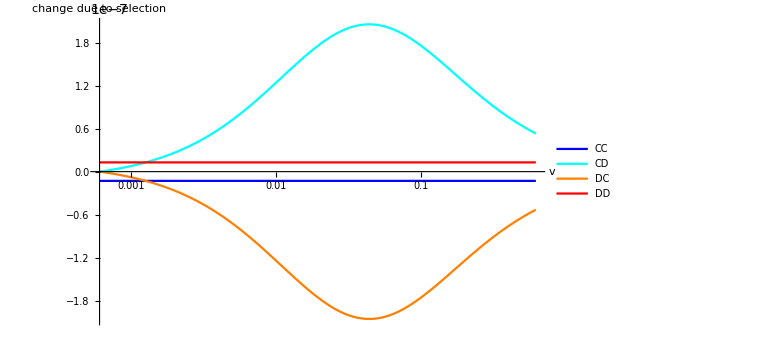

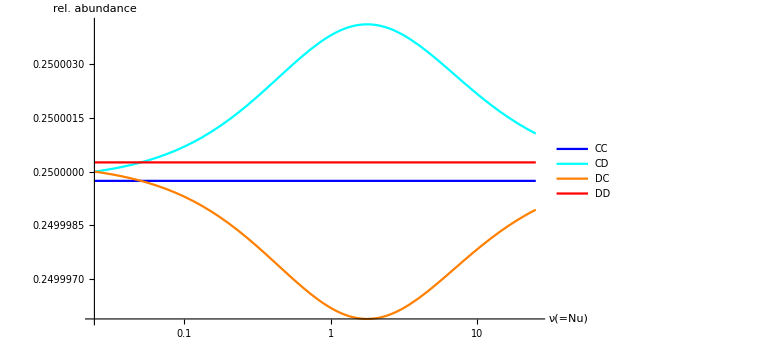

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=1.0;ββ=0.001;cc=0.2;bb=1.0;
μμ=nn*uu;

factor1=1;factor2=1;
μμ*factor1

plot1=LogLinearPlot[{
ΔxCC[nn,ββ,pp,bb,cc,μμ*factor1,nn*vv*factor2],
ΔxCD[nn,ββ,pp,bb,cc,μμ*factor1,nn*vv*factor2],
ΔxDC[nn,ββ,pp,bb,cc,μμ*factor1,nn*vv*factor2],
ΔxDD[nn,ββ,pp,bb,cc,μμ*factor1,nn*vv*factor2]},{vv,0,0.625},
AxesLabel->{"v","change due to selection"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}];

plot2=LogLinearPlot[{
1/4+(1-pp/2)ββ(nn(1-uu))/uu ΔxCC[nn,ββ,pp,bb,cc,μμ*factor1,ν*factor2],
1/4+(1-pp/2)ββ(nn(1-uu))/uu ΔxCD[nn,ββ,pp,bb,cc,μμ*factor1,ν*factor2],
1/4+(1-pp/2)ββ(nn(1-uu))/uu ΔxDC[nn,ββ,pp,bb,cc,μμ*factor1,ν*factor2],
1/4+(1-pp/2)ββ(nn(1-uu))/uu ΔxDD[nn,ββ,pp,bb,cc,μμ*factor1,ν*factor2]},{ν,0,0.625*nn},
AxesLabel->{"ν(=Nu)","rel. abundance"},PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625*nn},Automatic},
ImageSize->Large,PlotRange->All,PlotStyle->{Blue,Cyan,Orange,Red}];
plot1
plot2
```

```mathematica
Solve[1/4+(1/4 (bb+cc (-1+nn)) (-1+nn) (-1+y)/.{y->0.9807692})*x==0.21,x]
```

{{x→0.0242424}}

```mathematica
ββ(1-uu)/(nn*uu)
```

0.024975

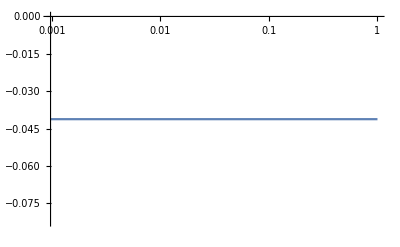

```mathematica
LogLinearPlot[ββ(1-uu)/(nn uu)ΔxCC[nn,ββ,pp,bb,cc,nn*uu,nn*vv],{vv,0,1}]
```